## Simulation setup

```mathematica
nxL = 100;
nxR = 100;
n=nxL+nxR;

x1=-10;
x2=10;

dx=(x2-x1)/(nxL+nxR);

(* initial values *)

initialValuesLeft = {0,0,0,0};
initialValuesRight={0,0,0,0,1};

W={};
For[i=0,i<nxL,i++,
values[i]=initialValuesLeft;
W=Join[W,values[i]];
];
values[nxL]=ArrayPad[initialValuesLeft,{0,1}];
W=Join[W,values[nxL]];
(*values[nxL,t,x]=initialValuesLeft;*)
For[i=1,i<=nxR+1,i++,
values[i+nxL]=initialValuesRight;
W=Join[W,values[i+nxL]];
];

dt=0.1dx;
time= 0.0;
step=0;

tend=2;
```

## Construction of the spatial discretization matrix

```mathematica
A3={{0, 1, 0, 0}, {1, 0, Sqrt[2], 0}, {0, Sqrt[2], 0, Sqrt[3]}, {0, 0, Sqrt[3], 0}};
ATilde={{0, 1, 0, 0, 0}, {1, 0, Sqrt[2], 0, 0}, {0, Sqrt[2], 0, Sqrt[3], 0}, {0, 0, Sqrt[3], 0, Sqrt[4]}, {0, 0, 0, 0, 0}};
A4={{0, 1, 0, 0, 0}, {1, 0, Sqrt[2], 0, 0}, {0, Sqrt[2], 0, Sqrt[3], 0}, {0, 0, Sqrt[3], 0, Sqrt[4]}, {0, 0, 0, Sqrt[4], 0}};

Q3=IdentityMatrix[4];
QTilde={{1, 0, 0, 0, 0}, {0, 1, 0, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 0, 1, 0}, {0, 0, 0, 0, 0}};
Q4=IdentityMatrix[5];

Roe = ConstantArray[0,{n+2,n+2}];
Viscosity=ConstantArray[0,{n+2,n+2}];

(* First row is a ghost row *)

For[j=1,j<=nxL,j++,
Roe[[1,j]]=ConstantArray[0,{4,4}];
Viscosity[[1,j]]=ConstantArray[0,{4,4}];
]

For[j=nxL+1,j<=n+2,j++,
Roe[[1,j]]=ConstantArray[0,{4,5}];
Viscosity[[1,j]]=ConstantArray[0,{4,5}];
]


(* Rows corresponding to moment model of order M *)

For[i=2,i<nxL,i++,
Roe[[i,i-1]]=A3;
Roe[[i,i]]=ConstantArray[0,{4,4}];
Roe[[i,i+1]]=-A3;
Viscosity[[i,i-1]]=-Q3;
Viscosity[[i,i]]=2*Q3;
Viscosity[[i,i+1]]=-Q3;

For[j=1,j<i-1,j++,
Roe[[i,j]]=ConstantArray[0,{4,4}];
Viscosity[[i,j]]=ConstantArray[0,{4,4}];
];

For[j=i+2,j<=nxL,j++,
Roe[[i,j]]=ConstantArray[0,{4,4}];
Viscosity[[i,j]]=ConstantArray[0,{4,4}];
];

For[j=nxL+1,j<=n+2,j++,
Roe[[i,j]]=ConstantArray[0,{4,5}];
Viscosity[[i,j]]=ConstantArray[0,{4,5}];
];
];

(* Row nxL (corresponds to vector nxL-1 because of the introduced ghost rows *) 

Roe[[nxL,nxL-1]]=A3;
Roe[[nxL,nxL]]=ConstantArray[0,{4,4}];
Roe[[nxL,nxL+1]]=-ArrayPad[A3,{{0,0},{0,1}}];
Viscosity[[nxL,nxL-1]]=-Q3;
Viscosity[[nxL,nxL]]=2*Q3;
Viscosity[[nxL,nxL+1]]=-ArrayPad[Q3,{{0,0},{0,1}}];

For[j=1,j<nxL-1,j++,
Roe[[nxL,j]]=ConstantArray[0,{4,4}];
Viscosity[[nxL,j]]=ConstantArray[0,{4,4}];
];

For[j=nxL+2,j<=n+2,j++,
Roe[[nxL,j]]=ConstantArray[0,{4,5}];
Viscosity[[nxL,j]]=ConstantArray[0,{4,5}];
];


(* Row nxL+1 (correspond to vector nxL because of the introduced  ghost rows *)

Roe[[nxL+1,nxL]]=ArrayPad[A3,{{0,1},{0,0}}];
Roe[[nxL+1,nxL+1]]=ConstantArray[0,{5,5}];
Roe[[nxL+1,nxL+2]]=-ATilde;
Viscosity[[nxL+1,nxL]]=-ArrayPad[Q3,{{0,1},{0,0}}];
Viscosity[[nxL+1,nxL+1]]=2*ArrayPad[Q3,{{0,1},{0,1}}];
Viscosity[[nxL+1,nxL+2]]=-QTilde;

For[j=1,j<nxL,j++,
Roe[[nxL+1,j]]=ConstantArray[0,{5,4}];
Viscosity[[nxL+1,j]]=ConstantArray[0,{5,4}];
];

For[j=nxL+3,j<=n+2,j++,
Roe[[nxL+1,j]]=ConstantArray[0,{5,5}];
Viscosity[[nxL+1,j]]=ConstantArray[0,{5,5}];
];

(* Row nxL+2 (corresponds to vector nxL+1 because of the introduced ghost rows *)

norm=0;
For[i=1,i<=4,i++,
norm+=(W[[4*nxL+i]]-W[[4*nxL+5+i]])^2;
];
If[Sqrt[norm]+Abs[W[[4*nxL+10]]]==0,s0=0,s0=Sqrt[norm]/(Sqrt[norm]+Abs[W[[4*nxL+10]]])];
WeightedSumRoe=s0*ATilde+(1-s0)*A4;
WeightedSumRoe[[All,5]]=0;
Roe[[nxL+2,nxL+1]]=WeightedSumRoe;
Roe[[nxL+2,nxL+2]]=s0*(ATilde-A4);
Roe[[nxL+2,nxL+3]]=-A4;
WeightedSumViscosity=s0*QTilde+(1-s0)*Q4;
WeightedSumViscosity[[All,5]]=0;
Viscosity[[nxL+2,nxL+1]]=-WeightedSumViscosity;
Viscosity[[nxL+2,nxL+2]]=2*Q4+s0*(QTilde-Q4);
Viscosity[[nxL+2,nxL+3]]=-Q4;

(*
Roe[[nxL+2,nxL+1]]=A4;
Roe[[nxL+2,nxL+2]]=ConstantArray[0,{5,5}];
Roe[[nxL+2,nxL+3]]=-A4;
Viscosity[[nxL+2,nxL+1]]=-Q4;
Viscosity[[nxL+2,nxL+2]]=2*Q4;
Viscosity[[nxL+2,nxL+3]]=-Q4;
*)

For[j=1,j<=nxL,j++,
Roe[[nxL+2,j]]=ConstantArray[0,{5,4}];
Viscosity[[nxL+2,j]]=ConstantArray[0,{5,4}];
];

For[j=nxL+4,j<=n+2,j++,
Roe[[nxL+2,j]]=ConstantArray[0,{5,5}];
Viscosity[[nxL+2,j]]=ConstantArray[0,{5,5}];
];


(* Rows corresponding to moment model of order M+1 (without the last one) *)

For[i=nxL+3,i<n+2,i++,
Roe[[i,i-1]]=A4;
Roe[[i,i]]=ConstantArray[0,{5,5}];
Roe[[i,i+1]]=-A4;

Viscosity[[i,i-1]]=-Q4;
Viscosity[[i,i]]=2*Q4;
Viscosity[[i,i+1]]=-Q4;

For[j=1,j<=nxL,j++,
Roe[[i,j]]=ConstantArray[0,{5,4}];
Viscosity[[i,j]]=ConstantArray[0,{5,4}];
];

For[j=nxL+1,j<i-1,j++,
Roe[[i,j]]=ConstantArray[0,{5,5}];
Viscosity[[i,j]]=ConstantArray[0,{5,5}];
];

For[j=i+2,j<=n+2,j++,
Roe[[i,j]]=ConstantArray[0,{5,5}];
Viscosity[[i,j]]=ConstantArray[0,{5,5}];
];
];


(* Last rows are ghost rows *)

For[j=1,j<=nxL,j++,
Roe[[n+2,j]]=ConstantArray[0,{5,4}];
Viscosity[[n+2,j]]=ConstantArray[0,{5,4}];
];

For[j=nxL+1,j<=n+2,j++,
Roe[[n+2,j]]=ConstantArray[0,{5,5}];
Viscosity[[n+2,j]]=ConstantArray[0,{5,5}];
];

RoeFlatten = ArrayFlatten[Roe];
ViscosityFlatten = ArrayFlatten[Viscosity];

BigAMatrix=-1/(2*dx)*(Roe+Viscosity);
BigAMatrixFlatten = -1/(2*dx)*(RoeFlatten+ViscosityFlatten);
```

## Simulation

```mathematica
While[time<tend,
(*
norm=0;
For[i=1,i<=4,i++,
norm+=(W[[4*nxL+i]]-W[[4*nxL+5+i]])^2;
];
If[Sqrt[norm]+Abs[W[[4*nxL+10]]]==0,s0=0,s0=Sqrt[norm]/(Sqrt[norm]+Abs[W[[4*nxL+10]]])];

WeightedSumRoe=s0*ATilde+(1-s0)*A4;
WeightedSumRoe[[All,5]]=0;
WeightedSumViscosity=s0*QTilde+(1-s0)*Q4;
WeightedSumViscosity[[All,5]]=0;

BigAMatrix[[nxL+2,nxL+1]]= -1/(2*dx)*(WeightedSumRoe-WeightedSumViscosity);
BigAMatrix[[nxL+2,nxL+2]]= -1/(2*dx)*(s0*(ATilde-A4)+2*Q4+s0*(QTilde-Q4));
BigAMatrix[[nxL+2,nxL+3]]= -1/(2*dx)*(-A4-Q4);
*)

BigAMatrix[[nxL+2,nxL+1]]= -1/(2*dx)*(A4-Q4);
BigAMatrix[[nxL+2,nxL+2]]= -1/(2*dx)*(2*Q4);
BigAMatrix[[nxL+2,nxL+3]]= -1/(2*dx)*(-A4-Q4);


BigAMatrixFlatten=ArrayFlatten[BigAMatrix];

W=W+dt*BigAMatrixFlatten.W;
time = time+dt;
]
```

## Numerical data post processing

```mathematica
m0={};
m1={};
m2={};
m3={};
m4={};
For[i=0,i<nxL,i++,
m0=Append[m0,W[[4*i+1]]];
m1=Append[m1,W[[4*i+2]]];
m2=Append[m2,W[[4*i+3]]];
m3=Append[m3,W[[4*i+4]]];
]
For[i=0,i<=nxR+1,i++,
m0=Append[m0,W[[4*nxL+5*i+1]]];
m1=Append[m1,W[[4*nxL+5*i+2]]];
m2=Append[m2,W[[4*nxL+5*i+3]]];
m3=Append[m3,W[[4*nxL+5*i+4]]];
m4=Append[m4,W[[4*nxL+5*i+5]]];
]
```

```mathematica
Dimensions[m2]//MatrixForm
```

(202)

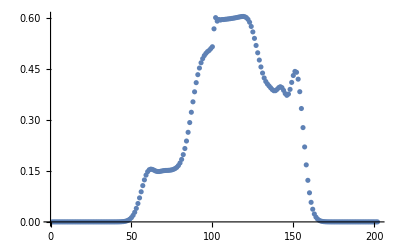

```mathematica
ListPlot[m3]
```

```mathematica
BigAMatrix//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/5 | -1/5 | 0 | 0 | -2/5 | 0 | 0 | 0 | 1/5 | 1/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/5 | 1/5 | -(√2)/5 | 0 | 0 | -2/5 | 0 | 0 | 1/5 | 1/5 | (√2)/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -(√2)/5 | 1/5 | -(√3)/5 | 0 | 0 | -2/5 | 0 | 0 | (√2)/5 | 1/5 | (√3)/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -(√3)/5 | 1/5 | 0 | 0 | 0 | -2/5 | 0 | 0 | (√3)/5 | 1/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/5 | -1/5 | 0 | 0 | -2/5 | 0 | 0 | 0 | 1/5 | 1/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/5 | 1/5 | -(√2)/5 | 0 | 0 | -2/5 | 0 | 0 | 1/5 | 1/5 | (√2)/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -(√2)/5 | 1/5 | -(√3)/5 | 0 | 0 | -2/5 | 0 | 0 | (√2)/5 | 1/5 | (√3)/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -(√3)/5 | 1/5 | 0 | 0 | 0 | -2/5 | 0 | 0 | (√3)/5 | 1/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/5 | -1/5 | 0 | 0 | -2/5 | 0 | 0 | 0 | 1/5 | 1/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/5 | 1/5 | -(√2)/5 | 0 | 0 | -2/5 | 0 | 0 | 1/5 | 1/5 | (√2)/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(√2)/5 | 1/5 | -(√3)/5 | 0 | 0 | -2/5 | 0 | 0 | (√2)/5 | 1/5 | (√3)/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(√3)/5 | 1/5 | 0 | 0 | 0 | -2/5 | 0 | 0 | (√3)/5 | 1/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/5 | -1/5 | 0 | 0 | -2/5 | 0 | 0 | 0 | 0 | 1/5 | 1/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/5 | 1/5 | -(√2)/5 | 0 | 0 | -2/5 | 0 | 0 | 0 | 1/5 | 1/5 | (√2)/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(√2)/5 | 1/5 | -(√3)/5 | 0 | 0 | -2/5 | 0 | 0 | 0 | (√2)/5 | 1/5 | (√3)/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(√3)/5 | 1/5 | 0 | 0 | 0 | -2/5 | 0 | 0 | 0 | (√3)/5 | 1/5 | 2/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/5 | -1/5 | 0 | 0 | 0 | -2/5 | 0 | 0 | 0 | 0 | 1/5 | 1/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/5 | 1/5 | -(√2)/5 | 0 | 0 | 0 | -2/5 | 0 | 0 | 0 | 1/5 | 1/5 | (√2)/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(√2)/5 | 1/5 | -(√3)/5 | 0 | 0 | 0 | -2/5 | 0 | 0 | 0 | (√2)/5 | 1/5 | (√3)/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(√3)/5 | 1/5 | 0 | 0 | 0 | 0 | -2/5 | 0 | 0 | 0 | (√3)/5 | 1/5 | 2/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2/5 | 0 | 0 | 0 | 0 | 0 | -2/5 | 0 | 0 | 0 | 2/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/5 | -1/5 | 0 | 0 | 0 | -2/5 | 0 | 0 | 0 | 0 | 1/5 | 1/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/5 | 1/5 | -(√2)/5 | 0 | 0 | 0 | -2/5 | 0 | 0 | 0 | 1/5 | 1/5 | (√2)/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(√2)/5 | 1/5 | -(√3)/5 | 0 | 0 | 0 | -2/5 | 0 | 0 | 0 | (√2)/5 | 1/5 | (√3)/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(√3)/5 | 1/5 | -2/5 | 0 | 0 | 0 | -2/5 | 0 | 0 | 0 | (√3)/5 | 1/5 | 2/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2/5 | 1/5 | 0 | 0 | 0 | 0 | -2/5 | 0 | 0 | 0 | 2/5 | 1/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/5 | -1/5 | 0 | 0 | 0 | -2/5 | 0 | 0 | 0 | 0 | 1/5 | 1/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/5 | 1/5 | -(√2)/5 | 0 | 0 | 0 | -2/5 | 0 | 0 | 0 | 1/5 | 1/5 | (√2)/5 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(√2)/5 | 1/5 | -(√3)/5 | 0 | 0 | 0 | -2/5 | 0 | 0 | 0 | (√2)/5 | 1/5 | (√3)/5 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(√3)/5 | 1/5 | -2/5 | 0 | 0 | 0 | -2/5 | 0 | 0 | 0 | (√3)/5 | 1/5 | 2/5 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2/5 | 1/5 | 0 | 0 | 0 | 0 | -2/5 | 0 | 0 | 0 | 2/5 | 1/5 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/5 | -1/5 | 0 | 0 | 0 | -2/5 | 0 | 0 | 0 | 0 | 1/5 | 1/5 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/5 | 1/5 | -(√2)/5 | 0 | 0 | 0 | -2/5 | 0 | 0 | 0 | 1/5 | 1/5 | (√2)/5 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(√2)/5 | 1/5 | -(√3)/5 | 0 | 0 | 0 | -2/5 | 0 | 0 | 0 | (√2)/5 | 1/5 | (√3)/5 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(√3)/5 | 1/5 | -2/5 | 0 | 0 | 0 | -2/5 | 0 | 0 | 0 | (√3)/5 | 1/5 | 2/5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2/5 | 1/5 | 0 | 0 | 0 | 0 | -2/5 | 0 | 0 | 0 | 2/5 | 1/5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Dimensions[BigAMatrix]
```

{46,46}

```mathematica
(*norm=0;
For[i=1,i<=4,i++,
norm+=(W[[4*nxL+i]]-W[[4*nxL+5+i]])^2;
];
If[Sqrt[norm]+Abs[W[[4*nxL+10]]]==0,s0=0,s0=Sqrt[norm]/(Sqrt[norm]+Abs[W[[4*nxL+10]]])];

WeightedSumRoe=s0*ATilde+(1-s0)*A4;
WeightedSumRoe[[All,5]]=0;
WeightedSumViscosity=s0*QTilde+(1-s0)*Q4;
WeightedSumViscosity[[All,5]]=0;

BigAMatrix[[nxL+2,nxL+1]]= -1/(2*dx)*(WeightedSumRoe-WeightedSumViscosity);
BigAMatrix[[nxL+2,nxL+2]]= -1/(2*dx)*(s0*(ATilde-A4)+2*Q4+s0*(QTilde-Q4));
BigAMatrix[[nxL+2,nxL+3]]= -1/(2*dx)*(-A4-Q4);*)

W=W+dt*BigAMatrix.W;
time = time+dt;
```

```mathematica
BigAMatrix.W//MatrixForm
```

(0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
1.11022×10^-16
0.
0.
0.
0.866025
0.5
0.
-5.55112×10^-17
0.866025
1.
0.
0.
0.
-0.866025
1.5
-1.5
0.
0.
-0.866025
1.
-1.25
0.
0.
0.
2.22045×10^-16
-1.11022×10^-16
0.
0.
0.
2.22045×10^-16
0.
0.
0.
0.
0.
0.)

```mathematica
Dimensions[BigAMatrix]
```

{46,46}

```mathematica
Dimensions[W]
```

{46}

```mathematica
BigAMatrix.Transpose[W]
```

Dot::rect: Nonrectangular tensor encountered.

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/5,-1/5,0,0,-2/5,0,0,0,1/5,1/5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},37,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}.{1,44,1}
 |  |  |  |

```mathematica
W//MatrixForm
```

(1)
 |  |  |  |